```mathematica
NotebookEvaluate[NotebookDirectory[]<>"/split_step.nb"];
```

GPE solver v1.4, RZ 2019

```mathematica
HarmonicTrap1D[];
sizes={1024};
timeStep=0.001;
k=-0.4;
contactInteractionFactor=4 Pi k;
initialize[];
gridReport
```

sizes | dim | len | max | min | delta | deltak | maxk
{1024} | 1 | 1024 | {5} | {-5} | {10/1023} | {(1023 π)/5120} | {(1023 π)/10}

time | energies | moments | misc
(0) | (total | -0.502651
kinetic | 0.25
potential | 0.25
contact | -1.00265
virial | -1.00265) | (meanX | 0
sigmaX | 0.707107
norm | 1.) | (steps | 0
A0 | 0.751126)

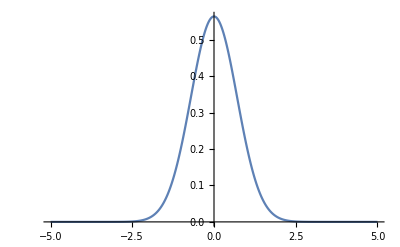

```mathematica
calcAllTable
p1=plotProjections
```

```mathematica
AbsoluteTiming[evolve["ite",10,10]]
```

{2.88498,Null}

time | energies | moments | misc
(10.) | (total | -0.991697
kinetic | 1.15541
potential | 0.0580686
contact | -2.20517
virial | -0.0104966) | (meanX | 0
sigmaX | 0.340789
norm | 1.) | (steps | 10000
A0 | 1.14402)

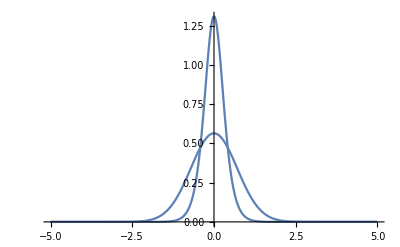

```mathematica
calcAllTable
p2=plotProjections;
Show[p1,p2,PlotRange->All]
```

```mathematica
reportMoments
```

time | meanX | sigmaX | norm
0 | 0 | 0.707107 | 1.
1. | 0 | 0.36095 | 1.
2. | 0 | 0.341444 | 1.
3. | 0 | 0.34081 | 1.
4. | 0 | 0.34079 | 1.
5. | 0 | 0.340789 | 1.
6. | 0 | 0.340789 | 1.
7. | 0 | 0.340789 | 1.
8. | 0 | 0.340789 | 1.
9. | 0 | 0.340789 | 1.
10. | 0 | 0.340789 | 1.

Turn off harmonic potential

```mathematica
newPotential[(0&)];
plot:=AppendTo[lplots,{time,plotProjections}];
reset[];
AbsoluteTiming[evolve["ite",5,20,20]]
```

{4.74684,Null}

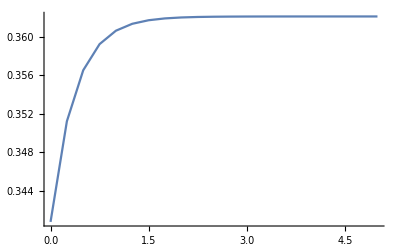

```mathematica
ListPlot[lmoments[[All,{1,3}]],Joined->True,PlotRange->All]
```

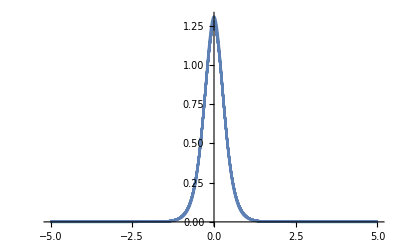

```mathematica
Show[lplots[[All,2]],PlotRange->All]
```

```mathematica
f=psi;
```

```mathematica
γ=contactInteractionFactor;
```

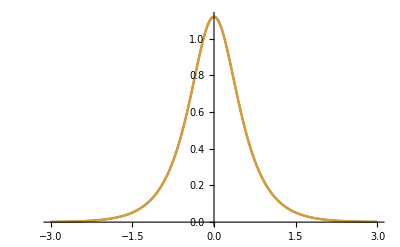

```mathematica
Plot[{Abs[f[x]],Sqrt[Abs[γ]/4]Sech[x Abs[γ]/2]},{x,-3,3},PlotRange->All]
```

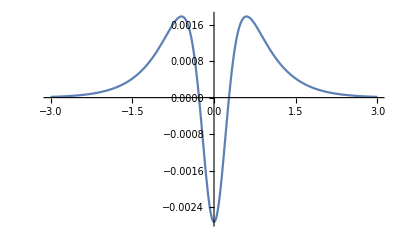

```mathematica
Plot[Abs[f[x]]-Sqrt[Abs[γ]/4]Sech[x Abs[γ]/2],{x,-3,3},PlotRange->All]
```

```mathematica
(* g=Abs[γ] *)
(* Enacba oblike -1/2 ψ''-g |ψ|^2 ψ==μ ψ *)
```

```mathematica
ψ=Sqrt[g/4]Sech[x g/2]
```

1/2 √g Sech[(g x)/2]

```mathematica
Integrate[ψ^2,{x,-∞,∞},Assumptions->g>0]
```

1

```mathematica
(-1/2)D[ψ,{x,2}]
x1=Simplify[%]
```

-1/4 √g (-1/4 g^2 Sech[(g x)/2]^3+1/4 g^2 Sech[(g x)/2] Tanh[(g x)/2]^2)

-1/32 g^(5/2) (-3+Cosh[g x]) Sech[(g x)/2]^3

```mathematica
(* Note the sign! *)
-g ψ^2 ψ
x2=Simplify[%]
```

-1/8 g^(5/2) Sech[(g x)/2]^3

-1/8 g^(5/2) Sech[(g x)/2]^3

```mathematica
xx=FullSimplify[x1+x2,g>0 && x∈Reals]
```

-1/16 g^(5/2) Sech[(g x)/2]

```mathematica
mu=xx/ψ
```

-g^2/8

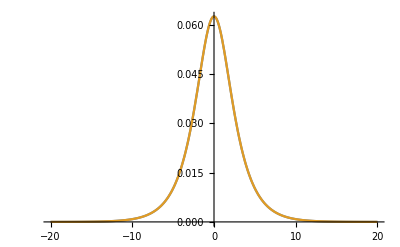

```mathematica
Plot[{-xx/.g->1,-mu ψ/.g->1},{x,-20,20},PlotRange->All]
```

```mathematica
Simplify[x1+x2]
mu ψ
```

-1/16 g^(5/2) Sech[(g x)/2]

-1/16 g^(5/2) Sech[(g x)/2]

```mathematica
(* Prefactor to x in Sech[...x] *)
Simplify[Sqrt[2 (-mu)],g>0]
```

g/2